## Simulation des stochastischen Kühlens (Teil 1)

#### Transportmatrizen

Die Transportmatrix zwischen Pickup (1) und Kicker (2) ausgedrückt durch die β-Funktionen

```mathematica
tmatgen = {{(β2/β1)^(1/2)(Cos[ψ]+α1 Sin[ψ]),(β1 β2)^(1/2)Sin[ψ]},{-(1+α1 α2)/(β1 β2)^(1/2)Sin[ψ]+(α1-α2)/(β1 β2)^(1/2)Cos[ψ],(β1/β2)^(1/2)(Cos[ψ]-α2 Sin[ψ])}}
```

{{√(β2/β1) (Cos[ψ]+α1 Sin[ψ]),√(β1 β2) Sin[ψ]},{((α1-α2) Cos[ψ])/(√(β1 β2))+((-1-α1 α2) Sin[ψ])/(√(β1 β2)),√(β1/β2) (Cos[ψ]-α2 Sin[ψ])}}

Vereinfacht sich wenn man sich auf ψ = π/2 beschränkt

```mathematica
tmat90= tmatgen /. ψ->π/2
```

{{α1 √(β2/β1),√(β1 β2)},{(-1-α1 α2)/(√(β1 β2)),-α2 √(β1/β2)}}

Die Matrix für den Rest des Umlaufs, also von (2) nach (1) erhält man allgemein so :

```mathematica
tmatrest = tmatgen /. {β2->β1,β1->β2,α2->α1,α1->α2, ψ->μ-ψ}
```

{{√(β1/β2) (Cos[μ-ψ]+α2 Sin[μ-ψ]),√(β1 β2) Sin[μ-ψ]},{((-α1+α2) Cos[μ-ψ])/(√(β1 β2))+((-1-α1 α2) Sin[μ-ψ])/(√(β1 β2)),√(β2/β1) (Cos[μ-ψ]-α1 Sin[μ-ψ])}}

und auch hier wieder für den ψ = π/2 Fall :

```mathematica
tmatrest90= tmatrest  /. ψ->π/2//Simplify
```

{{√(β1/β2) (-α2 Cos[μ]+Sin[μ]),-√(β1 β2) Cos[μ]},{((1+α1 α2) Cos[μ]+(-α1+α2) Sin[μ])/(√(β1 β2)),√(β2/β1) (α1 Cos[μ]+Sin[μ])}}

Das Produkt sollte die Twiss Matrix am Ort (1) sein :

```mathematica
FullSimplify[tmatrest.tmatgen,{β1>0,β2>0}]
```

{{Cos[μ]+α1 Sin[μ],β1 Sin[μ]},{-((1+α1^2) Sin[μ])/β1,Cos[μ]-α1 Sin[μ]}}

#### Definition des Gains

Für die übliche Definition des "gains" betrachten wir ein Pseudoteilchen, dass am Ort des Pickups eine Ablage x_p und x_p'=0 hat. Dieses transportieren wir zum Ort des Kickers

```mathematica
{xk,xkp} = tmat90.{xp,0}
```

{xp α1 √(β2/β1),(xp (-1-α1 α2))/(√(β1 β2))}

wie erwartet ist das x_k' (am Ort des Kickers) propportional zu x_p. Ein Kick der Stärke "1" ist dann definiert als (x')_kick= -1*(x_k'/x_p) x_mean wenn x_mean der vom pick-up gemessene mittlere offset der Teilchen ist.

```mathematica
ClearAll[g1kick]
```

```mathematica
g1kick[xm_] = -xkp/xp*xm
```

-(xm (-1-α1 α2))/(√(β1 β2))

#### Simulation

Mehr oder minder zufällige Parameter für die optischen Funktionen.

```mathematica
params = {β1->18.8,β2->10.6,α1->0.,α2->0.,ϵ->3.*10^-8, μ->23.27409747201 }
```

{β1→18.8,β2→10.6,α1→0.,α2→0.,ϵ→3.×10^-8,μ→23.2741}

Wir definieren die numerischen Transportmatrizen und die g=1 Kickstärke

```mathematica
tmat90num = tmat90 /. params;
```

```mathematica
tmatrest90num = tmatrest90 /. params;
```

```mathematica
g1kicknum[xm_] = g1kick[xm] /. params
```

0.0708383 xm

Checking the Twiss matrix ...

```mathematica
twissnum = tmatrest90num.tmat90num
```

{{-0.283889,-18.0265},{0.051003,-0.283889}}

```mathematica
Det[twissnum]
```

1.

```mathematica
Tr[twissnum]
```

-0.567778

ok, die Spur ist dem Betrag nach < 2, d.h. das ist eine stabile Optik.

Wir erzeugen einen angepassten Stahl aus n Teilchen, d.h. die Korrelationsmatrix muss mit der Beam-Matrix übereinstimmen:

```mathematica
Bmat = ϵ*{{β1,-α1},{-α1,γ1}} /. γ1->(1+α1^2)/β1 /. params
```

{{5.64×10^-7,0.},{0.,1.59574×10^-9}}

Damit man überhaupt einen Effekt sieht setzten wir die Mittelwerte <x> und <x'> nicht auf Null sondern endliche Werte. Sagen wir 1 mm und 0.1 mrad.

```mathematica
meanstart = {0.001,0.0001}
```

{0.001,0.0001}

```mathematica
start[n_] :=RandomReal[MultinormalDistribution[meanstart,Evaluate[Bmat]],n]
```

```mathematica
start[10]
```

{{0.0000339254,0.0000488537},{0.00237456,0.000170283},{0.00128574,0.0000864728},{0.000168685,0.0000536389},{0.000851516,0.000101951},{0.0010731,0.000100357},{0.00150342,0.0000918617},{0.0013097,0.0000903369},{-0.0000523758,0.0000985084},{0.00076458,0.0000956359}}

Ok, funktioniert.

Jetzt definieren wir die Funktion für einmal rum : 
- Berechnung der mittleren Ablage
- Transport zum Kicker
- Appliziere den Gegenkick
- Transport zurück zum Pickup

Weil wir das später vielleicht brauchen habe ich gleich die Möglichkeit eingebaut, ein Rauschen des Systems zu erlaube. Ausgedrückt wäre das in Auflösung der Pickup Messung...

```mathematica
round [set_,g_,noise_:0] := Block[{set1,set2,set3,mean},
mean = If[noise >0,Mean[set[[All,1]]]+RandomReal[NormalDistribution[0,noise]],Mean[set[[All,1]]]];
set1 =tmat90num .#& /@ set;
set2 =Plus[{0,g*g1kicknum[mean] },#]& /@ set1;
set3 = tmatrest90num .#& /@ set2;
Return[set3]
]
```

#### Erster Test

Nur 10 Teilchen, sagen wir 30 Umläufe...

```mathematica
set1 = start[10];
```

```mathematica
turns1 = NestList[round[#,1.,0]&,set1,30];
```

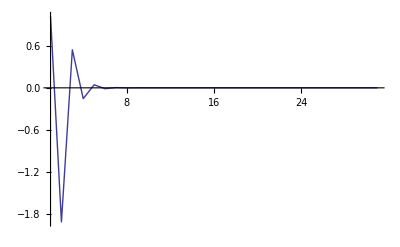

```mathematica
ListPlot[Mean /@ turns1[[All,All,1]]*1000, Joined->True, PlotRange->All, PlotTheme->"Scientific",FrameLabel->{"turn","<x> [mm]"}]
```

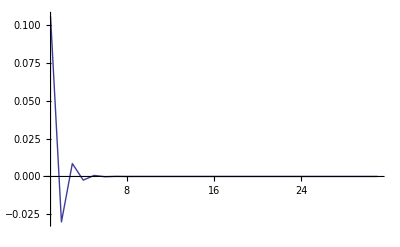

```mathematica
ListPlot[Mean /@ turns1[[All,All,2]]*1000, Joined->True, PlotRange->All, PlotTheme->"Scientific",FrameLabel->{"turn","<x'> [mrad]"}]
```

wie man sieht werden sowohl die mittlere Ablage wie auch das mittlere x' innerhalb weniger Umläufe auf Null gezogen.

Nehmen wir jetzt mal 1000 Teilchen

```mathematica
set11 = start[1000];
```

Wieder 30mal rum, ohne Rauschen

```mathematica
turns11 = NestList[round[#,1.,0]&,set11,30];
```

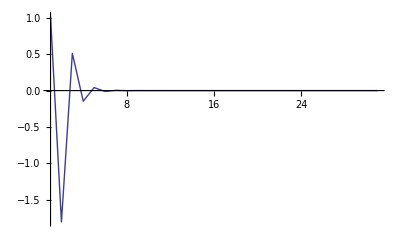

```mathematica
ListPlot[Mean /@ turns11[[All,All,1]]*1000, Joined->True, PlotRange->All, PlotTheme->"Scientific",FrameLabel->{"turn","<x> [mm]"}]
```

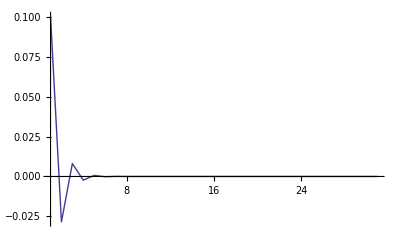

```mathematica
ListPlot[Mean /@ turns11[[All,All,2]]*1000, Joined->True, PlotRange->All, PlotTheme->"Scientific",FrameLabel->{"turn","<x'> [mrad]"}]
```

Man sieht praktisch keinen Unterschied, d.h. das "Einschwingen" auf Null ist kein statistischer Prozess sondern druch die Rückkopplung über die Transportmatrizen definiert. 
Wie sieht denn der Betrag der Ablage aus, das kann man mal Log darstellen:

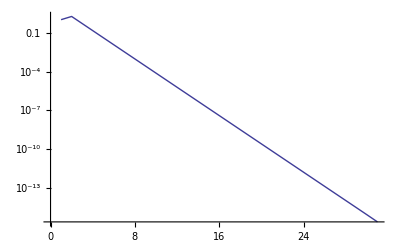

```mathematica
ListLogPlot[Abs[Mean /@ turns11[[All,All,1]]*1000.], Joined->True, PlotRange->All, PlotTheme->"Scientific",FrameLabel->{"turn","<x> [mm]"}]
```

aha, das nimmt also immer weiter ab. 
Machen wir mal 300 Umläufe :

```mathematica
turns300 = NestList[round[#,1.,0]&,set11,300];
```

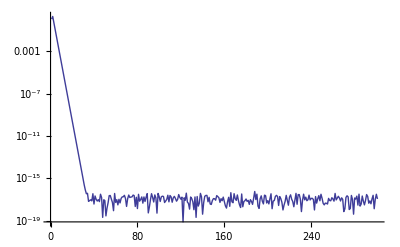

```mathematica
ListLogPlot[Abs[Mean /@ turns300[[All,All,1]]*1000.], Joined->True, PlotRange->All, PlotTheme->"Scientific",FrameLabel->{"turn","<x> [mm]"}]
```

Die Grenze ist hier durch die numerische "Auflösung" des Rechners bestimmt. Setzen wir mal eine realistische Auflösung der pickup Messung ein, sagen wir 1 µm:

```mathematica
turns300noise = NestList[round[#,1.,1.*10^-6]&,set11,300];
```

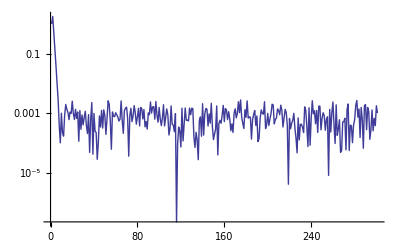

```mathematica
ListLogPlot[Abs[Mean /@ turns300noise[[All,All,1]]*1000.], Joined->True, PlotRange->All, PlotTheme->"Scientific",FrameLabel->{"turn","<x> [mm]"}]
```

dann bleiben wir dann damit bei einem deutlich größeren Mittelwert hängen.  Hängt das von der Anzahl der Teilchen ab ? 
Also probeweise mal nur 100 Teilchen:

```mathematica
set100 =start[100];
```

```mathematica
turns300noise100 = NestList[round[#,1.,1.*10^-6]&,set100,300];
```

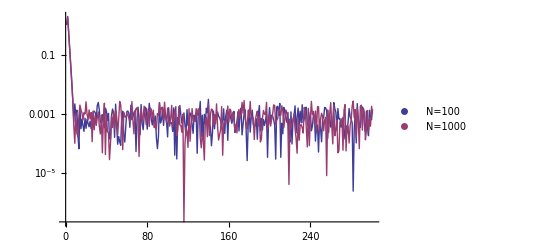

```mathematica
ListLogPlot[{Abs[Mean /@ turns300noise100[[All,All,1]]*1000.],Abs[Mean /@ turns300noise[[All,All,1]]*1000.]}, Joined->True, PlotRange->All, PlotTheme->"Scientific",FrameLabel->{"turn","<x> [mm]"}, PlotLegends->{"N=100","N=1000"}]
```

Offenbar nicht. Wovon es abhängt weiss ich auch nicht.

### Emittanz

Wird das "Ensemble" nun eigentlich gekühlt, d.h. nimmt die Emittanz des Strahls ab ? 
Dazu berechnen wir diese nach ihrer statistischen Definition:

```mathematica
emi[set_] := With[{setx = set[[All,1]],setxp = set[[All,2]]},(Mean[(setx)^2]* Mean[(setxp)^2]-Mean[(setx*setxp)]^2)^(1/2)]
```

Und betrachten uns das am Beispiel ohne Rauschen des Systems:

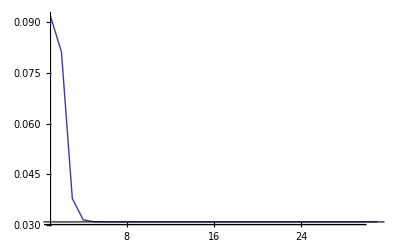

```mathematica
ListPlot[emi /@ turns11*10^6, Joined->True, PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"turn","ϵ[mm mrad]"},Epilog->{Line[{{0.,0.03},{30.,0.03}}]}]
```

Man sieht, die Emittanz ist am Anfang größer (!) als der hineingesteckte Wert, das liegt daran dass wir das Ensemble künstlich gegen {x,x'}={0,0} versetzt habe. Das feed-back System korrigiert das, die Emittanz geht auf den Sollwert von 3*10^-8 m fällt aber nicht weiter.  Erstaulicherweise fällt sie ganz leicht unter den Eingangswert, was das nun wieder bedeutet...

#### Kühlen :

Kommt dann im nächsten Aufgabenblatt.

```mathematica
newpart= start[1000];
```

bestimme nun für jedes Teilchen den notwendingen Kick

```mathematica
(*indkicktest=g1kicknum[#]&/@ newpart[[All, 2]];*)
```

```mathematica
(*GaussianFilter[indkicktest,2]; (*müssen wir den radius noch berechnen ??? kA was wir da eingeben sollen*)*)
```

```mathematica
(*round [set_,g_,noise_:0] := Block[{set1,set2,set3,mean},
mean = If[noise >0,Mean[set[[All,1]]]+RandomReal[NormalDistribution[0,noise]],Mean[set[[All,1]]]];
set1 =tmat90num .#& /@ set;
set2 =Plus[{0,g1kicknum[mean] },#]& /@ set1;
set3 = tmatrest90num .#& /@ set2;
Return[set3]
]*)
```

```mathematica
roundindkick[set_,g_,noise_:0] := Block[{setnew,set1,set2,set3,indkick,indkickg},
(*setnew = If[noise >0,set[[All,1]]+RandomReal[NormalDistribution[0,noise]],set[[All,1]]];*)
indkick=g*g1kicknum[#]&/@ set[[All, 1]];(*da g1kicknum nicht vom Gain abhängt, aber der ja variiert werden sollte*)
indkickg=GaussianFilter[indkick,2];
set1 =tmat90num .#& /@ set;
set2 =MapThread[Plus[{0,#1},#2]&,{indkickg,set1}];(*Plus[{0,g1kicknum[indkick] },#]& /@ set1;*)(*jeder individuelle kick wird auf das entsprechende teilchen dazu addiert*)
set3 = tmatrest90num .#& /@ set2;
Return[set3]
]
```

```mathematica
mix[set_,M_] := Block[{n,mixset,endset,localset},
localset=set;
n=Round[Length[localset]/M];
mixset=RandomSample[Range@Length@localset,n];
endset=RandomSample@mixset;
localset[[mixset]]=localset[[endset]];
Return[localset]
]
```

```mathematica
roundIndyMix[set_, g_, M_] := Module[{localset},
localset = set;
localset = roundindkick[localset, g];
localset = mix[localset, M];
Return[localset]
]
```

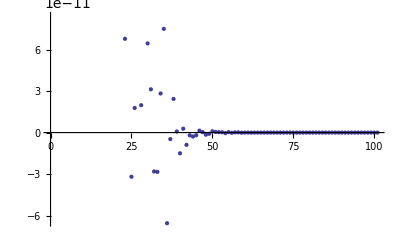

```mathematica
ListPlot[Mean/@NestList[roundIndyMix[#,  1, 1]&, newpart, 100][[All,All,1]]]
```

```mathematica
Manipulate[ListLogPlot[emi /@NestList[roundIndyMix[#,  g, 1]&, newpart, 100]*10^6], {g,0, 5, 0.1}]
```

Ab einem Gain von etwa 2 ist der Kick zu stark, sodass sich nach einigen zehn Umdrehungen die Emittanz wieder erhöht. Bei negativen Gains verstärkt der Kick die Abweichung, weshalb sie nicht mitgeplottet werden.

```mathematica
Manipulate[
ListLogPlot[emi /@NestList[roundIndyMix[#,  1, M]&, newpart, 100], PlotRange->{{0,100},{10^-25,10^-6}}], {M, 1, 100, 1}]
```

Die Emittanz nimmt mit steigendem M zunächst stark ab, um dann nach wenigen Umläufen ein bisschen langsamer exponentiell zu sinken, je kleiner M, desto stärker. Allerdings werden schon nach wenigen Umdrehungen unphysikalische Werte erreicht.

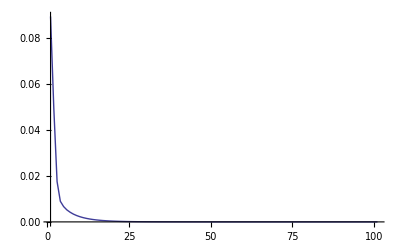

```mathematica
ListLinePlot[emi /@NestList[roundindkick[#,  1, 1]&, newpart, 100]*10^6,PlotRange->All]
```

```mathematica
coolingTime[emittanceList_]:=Position[emittanceList,Nearest[emittanceList, emittanceList[[1]]*Exp[-1]][[1]]]
```

```mathematica
elist[g_, M_] := emi /@NestList[roundIndyMix[#,  g, M]&, newpart, 100];
```

```mathematica
refTime1 =coolingTime[elist[1, 1]][[1, 1]]
```

3

```mathematica
(*Plot[{1/coolingTime[elist[g, M]],(2*g-g^2)*M/refTime1}//.M-> 1, {g, 0, 1}]*)
```

Der Verlauf der berechneten Kühlzeiten stimmt ungefähr mit dem Verlauf der Formel aus dem Skript überein.

```mathematica
Plot[{1/coolingTime[elist[g, M]],(2*g-g^2)*M/refTime1}//.g-> 1, {M, 1, 50}]
```